## Read in and interpolate data from simulations

## Read in

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bovyn/ownCloud/Projects/Bile Canaliculi mechanics/surface_evolver/main_text_fig

```mathematica
rawimport=Import["max_expansion_w_cut_depth/expansions.csv"];
```

```mathematica
rawimport10=Import["max_expansion_w_cut_depth/around10/expansions.csv"];
```

```mathematica
datao=Dataset@MapThread[<|"d"->#1,rawimport[[1,2]]->#2,rawimport[[1,3]]->#3|>&,{rawimport[[2;;-1,1]],rawimport[[2;;-1,2]],rawimport[[2;;-1,3]]}]
```

```mathematica
data10=Dataset@MapThread[<|"d"->#1,rawimport10[[1,2]]->#2,rawimport10[[1,3]]->#3|>&,{rawimport10[[2;;-1,1]],rawimport10[[2;;-1,2]],rawimport10[[2;;-1,3]]}]
```

```mathematica
data=Join[datao,data10[Select[#modulus!=10&&#modulus!=21.5&&#modulus!=46.4&&#modulus!=4.64&]]]
```

```mathematica
ds=DeleteDuplicates[Normal[data[All,"d"]]]
```

{0.327778,0.263194,0.198611,0.134028,0.0694444}

## Find maximum c for each depth

```mathematica
findcmaxs[j_]:=Module[{ddata,dinterppoints,dinterp,dsp,dmaxc},
ddata=data[Select[#d==ds[[j]]&]];
dinterppoints=Table[{Log[ddata[i,"modulus"]],ddata[i,"expansion_ratio"]},{i,1,Length[ddata]}]//Sort;
dinterp=Interpolation[dinterppoints];
dsp=BSplineFunction[Table[dinterp[c],{c,Log[.01],Log[100],(Log[100]-Log[.01])/50}]];
dmaxc=FindMaximum[{dsp[c],0<c<1},{c,.9}];
{Exp[c*(Log[100]-Log[.01])+Log[.01]]/.dmaxc[[2]],Show[LogLinearPlot[dsp[(Log[c]-Log[.01])/(Log[100]-Log[.01])],{c,.01,100},PlotRange->All],
ListLogLinearPlot[Table[{ddata[i,"modulus"],ddata[i,"expansion_ratio"]},{i,1,Length[ddata]}]],
ListLogLinearPlot[Table[{Exp[c],dinterp[c]},{c,Log[.01],Log[100],(Log[100]-Log[.01])/50}],PlotStyle->Orange]
],
dsp[(Log[c]-Log[.01])/(Log[100]-Log[.01])]}
]
```

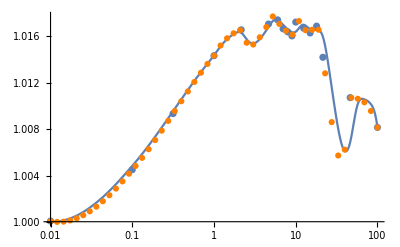
{12.363,-Graphics-,BSplineFunction[…][0.108574 (4.60517+Log[c])]}

```mathematica
findcmaxs[5]
```

```mathematica
findcmaxs[5][[2]]
```

-Graphics-

```mathematica
maxfinds=Table[findcmaxs[i],{i,1,5}];
```

```mathematica
cmaxs={20,findcmaxs[2][[1]],findcmaxs[3][[1]],findcmaxs[4][[1]],7}
```

{20,11.7788,12.8009,7.57896,7}

```mathematica
cmaxfiteq=a+b d
```

a+b d

```mathematica
cmaxfit=FindFit[Transpose[{ds,cmaxs}],cmaxfiteq,{a,b},d]
```

{a→2.54446,b→46.7611}

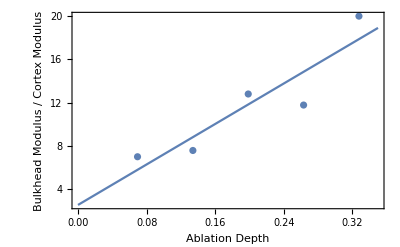

```mathematica
Show[
Plot[a+b d/.cmaxfit,{d,0,.35},PlotRange->{{0,All},{0,23}},Frame->True,FrameLabel->{"Ablation Depth","Bulkhead Modulus / Cortex Modulus"}],
ListPlot[Transpose[{ds,cmaxs}]]]
```

```mathematica
er==maxfiteq
```

er==1+d^2 y+d z

```mathematica
maxerofc=maxfiteq/.Solve[c==cmaxfiteq,d]//First
```

1+((-a+c)^2 y)/b^2+((-a+c) z)/b

```mathematica
correction=1-maxerofc/.maxfitmod["BestFitParameters"]/.cmaxfit/.c->0
```

0.0065819

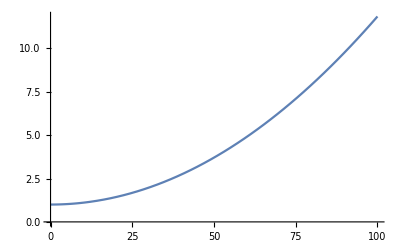

```mathematica
Plot[correction+maxerofc/.maxfitmod["BestFitParameters"]/.cmaxfit,{c,0,100}]
```

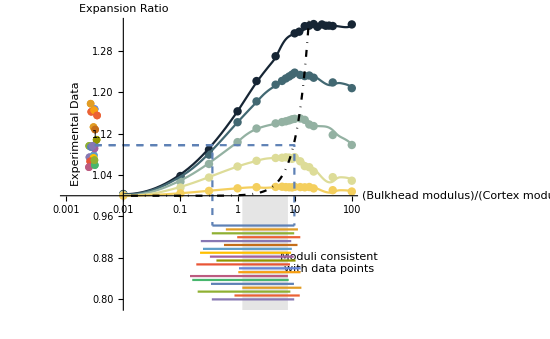

```mathematica
dmincmaxplot=Show[ListLogLinearPlot[Table[Transpose[{data[Select[#d==ds[[i]] &],"modulus"],data[Select[#d==ds[[i]] &],"expansion_ratio"]}//Normal],{i,1,5}],PlotRange->{{.001,Automatic},{.79,Automatic}},AxesOrigin->{.01,1},AxesLabel->{("Bulkhead modulus")/("Cortex modulus"),"Expansion Ratio"},LabelStyle->{FontSize->12,FontColor->Black},PlotStyle->"StarryNightColors",PlotRangeClipping->False,AxesStyle->AbsoluteThickness[1.02],PlotLegends->Placed[LineLegend[Round[ds*3.6*1.5,.01],LegendLabel->"Ablation Depth (μm)",LabelStyle->FontSize->11,Spacings->0],Scaled[{1.01,.85}]],ImageSize->{550,300},Epilog->{Inset[Rotate[Text["Experimental Data"],90 Degree],{-6.5,1.12}],Text[Style["Moduli consistent
with data points",TextAlignment->Left],{3.7,.87}]}],
(*LogLinearPlot[erinterp[Log[c],d]/.d->ds//Evaluate,{c,.01,100},PlotStyle->"StarryNightColors"],*)
LogLinearPlot[Table[maxfinds[[i]][[3]],{i,1,5}]//Evaluate,{c,.01,100},PlotStyle->"StarryNightColors"],
LogLinearPlot[correction+maxerofc/.maxfitmod["BestFitParameters"]/.cmaxfit,{c,.01,100},PlotStyle->{Black,DotDashed},PlotLegends->Placed[LineLegend[{"Min Ablation"},LabelStyle->FontSize->10],Scaled[{1.01,.85}]]],
LogLinearPlot[.7,{c,1.212928192904417,Min[csdmin]},PlotStyle->Gray,Filling->1],
ListLinePlot[rangelines,ScalingFunctions->{"Log"}],
ListPlot[erpoints,ScalingFunctions->{"Log"},PlotStyle->PointSize->.01],
ListLogLinearPlot[{erpoints[[1,1]],{csdmax[[1]],inferencedata[[1]]},rangelines[[1,2]]},Joined->True,PlotStyle->Dashed],
ListLogLinearPlot[{erpoints[[1,1]],{csdmin[[1]],inferencedata[[1]]},rangelines[[1,1]]},Joined->True,PlotStyle->Dashed]
]
```

```mathematica
Export["supps/dmincmax.pdf",dmincmaxplot]
```

supps/dmincmax.pdf